Logistic Model script

```mathematica
Clear["Global`*"]
```

```mathematica
Adot = r*A*(1-A/k)-α*A*L
```

A (1-A/k) r-A L α

```mathematica
Ldot=-c*L+β*A*L
```

-c L+A L β

```mathematica
Solve[Adot==0,A]
```

{{A→0},{A→(k r-k L α)/r}}

```mathematica
Solve[Ldot==0,L]
```

{{L→0}}

```mathematica
Solve[{Adot==0,Ldot==0},{A,L}]
```

{{A→c/β,L→-(r (c-k β))/(k α β)},{A→0,L→0},{A→k,L→0}}

```mathematica
eq=Solve[{Adot/A==0,Ldot/L==0},{A,L}]
```

{{A→c/β,L→-(r (c-k β))/(k α β)}}

```mathematica
Aeq=A/.eq
```

{c/β}

```mathematica
Leq=L/.eq
```

{-(r (c-k β))/(k α β)}

Evaluate the Jacobian matrix of the system at the equilibrium for a local approximation.

```mathematica
jacobian=D[{Adot,Ldot},{{A,L}}]
```

{{(1-A/k) r-(A r)/k-L α,-A α},{L β,-c+A β}}

```mathematica
MatrixForm[jacobian]
```

((1-A/k) r-(A r)/k-L α | -A α
L β | -c+A β)

```mathematica
MatrixForm[jacobian/.{A->Aeq,L->Leq}]
```

((r (1-c/(k β))-(c r)/(k β)+(r (c-k β))/(k β)) | (-(c α)/β)
(-(r (c-k β))/(k α)) | (0))

```mathematica
r=0.21;
α=0.13;
c=0.10;
β=0.08;
k=3;
```

```mathematica
Eigenvalues[jacobian]/.{A->0,L->0}
```

{-0.1,0.21}

```mathematica
Eigenvalues[jacobian]/.{A->k,L->0}
```

{-0.21,0.14}

```mathematica
Eigenvalues[jacobian]/.{A->Aeq,L->Leq}
```

{{-0.04375-0.101666 ⅈ},{-0.04375+0.101666 ⅈ}}

I couldn’t get a manipulable to work, but the eigenvalues are of the form -a plus or minus bi for all carrying capacities I tried.

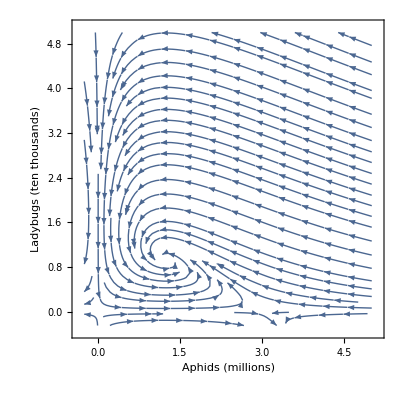

```mathematica
StreamPlot[{Adot,Ldot},{A,-0.25,5},{L,-0.25,5},Axes->True,AxesLabel->{"A","L"},Frame->True,FrameLabel->{"Aphids (millions)","Ladybugs (ten thousands)"},ImageSize->Full]
```

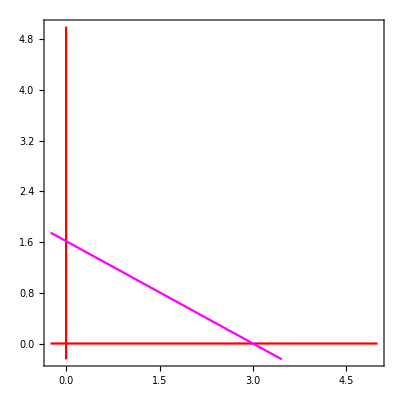

```mathematica
ContourPlot[{A==0,L==0,A==(3*0.21-3*L*0.13)/0.21},{A,-0.25,5},{L,-0.25,5},ContourStyle->{Red,Red,Magenta}]
```

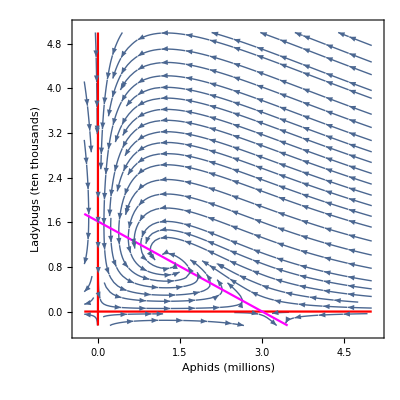

```mathematica
Show[StreamPlot[{Adot,Ldot},{A,-0.25,5},{L,-0.25,5},Axes->True,AxesLabel->{"A","L"},Frame->True,FrameLabel->{"Aphids (millions)","Ladybugs (ten thousands)"},ImageSize->Full],ContourPlot[{A==0,L==0,A==(k*0.21-k*L*0.13)/0.21},{A,-0.25,5},{L,-0.25,5},ContourStyle->{Red,Red,Magenta}],LabelStyle->{Black,30},ImageSize->Full]
```

```mathematica
Aeq
```

{1.25}

```mathematica
Leq
```

{0.942308}